## Solutions S_11and S_12

```mathematica
ClearAll["Global`*"]
```

```mathematica
bar[I0_,Ak_]:=I0*Ak;
(* The Intrinsic Spin terms *)
Subscript[P, 31][Spin_,j_,I0_,A1_,A3_]:=(2Spin-1)(bar[I0,A3]-bar[I0,A1])+2*j*bar[I0,A1];
Subscript[P, 21][Spin_,j_,I0_,A1_,A2_]:=(2Spin-1)(bar[I0,A2]-bar[I0,A1])+2*j*bar[I0,A1];
(* The Single-particle terms *)
Subscript[Q, 31][Spin_,j_,I0_,A1_,A3_]:=(2j-1)(bar[I0,A3]-bar[I0,A1])+2Spin*bar[I0,A1];
Subscript[Q, 21][Spin_,j_,I0_,A1_,A2_]:=(2j-1)(bar[I0,A2]-bar[I0,A1])+2Spin*bar[I0,A1];
(* The triaxial terms *)
Subscript[G, 1][j_,γ_]:=(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]);
Subscript[G, 2][j_,γ_]:=(2j-1)/(j(j+1))2 √3 Sin[γ*π/180];
```

### Equation for B=0

```mathematica
F0[I0_,V_,Spin_,j_,γ_,A1_,A2_,A3_]:=Subscript[G, 1][j,γ]*Subscript[G, 2][j,γ]*(I0*V)^2+(Subscript[Q, 21][Spin,j,I0,A1,A2]*Subscript[G, 1][j,γ]+Subscript[Q, 31][Spin,j,I0,A1,A3]*Subscript[G, 2][j,γ])*(I0*V)+Subscript[P, 31][Spin,j,I0,A1,A3]*Subscript[P, 21][Spin,j,I0,A1,A2]+8*Spin*j*bar[I0,A2]*bar[I0,A3];
```

### Numerical parameters

```mathematica
ak={1,0.3,3};
sp=35/2;
gm=25;
jj=13/2;
```

```mathematica
solutionF=Values@Solve[F0[x,y,sp,jj,gm,ak[[1]],ak[[2]],ak[[3]]]==0,{x,y}][[3,1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

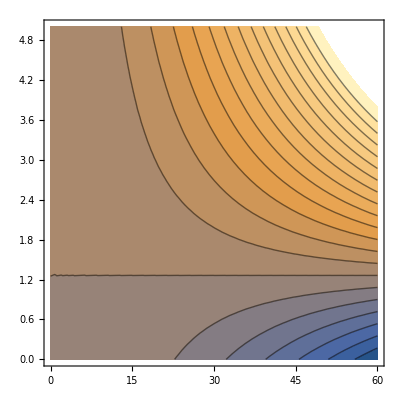

```mathematica
ContourPlot[F0[x,y,sp,jj,gm,ak[[1]],ak[[2]],ak[[3]]],{x,0,60},{y,0,5},Contours->20]
```